```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data = Import["../../../runs/Trials/N9K9/21385198.dat"];
```

```mathematica
data2 = Import["../../../runs/Trials/N9K9/15650383.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
cmatdata = cMatOne/@data;
```

```mathematica
eig = Flatten[Map[Eigenvalues, cmatdata[[All, 2;;]], {2}]];
```

```mathematica
randmat = Partition[(# - 1/($N)Tr[#]IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[σ/(√($N)), $N], Length[data]*$K], $K];
```

```mathematica
randeig = Flatten[Map[Eigenvalues, randmat, {2}]];
```

```mathematica
trX1X2 = Tr[#[[1]].#[[2]]]&/@cmatdata[[All, 2;;]]//Chop;
```

```mathematica
trX1X2rand = Tr[#[[1]].#[[2]]]&/@randmat//Chop;
```

```mathematica
x112Re = Re[#[[1, 1, 2]]]&/@cmatdata[[All, 2;;]]//Chop;
```

```mathematica
x112Rerand= Re[#[[1, 1, 2]]]&/@randmat//Chop;
```

```mathematica
x433 = Re[#[[4, 3, 3]]]&/@cmatdata[[All, 2;;]]//Chop;
x433rand= Re[#[[4, 3, 3]]]&/@randmat//Chop;
```

```mathematica
trX1sq = Tr[#[[1]].#[[1]]]&/@cmatdata[[All, 2;;]]//Chop;
trX1sqrand = Tr[#[[1]].#[[1]]]&/@randmat//Chop;
```

```mathematica
trXsq = Sum[Tr[#[[α]].#[[α]]]&/@cmatdata[[All, 2;;]]//Chop, {α, 1, $K}];
trXsqrand = Sum[Tr[#[[α]].#[[α]]]&/@randmat//Chop, {α, 1, $K}];
```

```mathematica
σ =StandardDeviation[x112Re]/StandardDeviation[x112Rerand]
```

0.18533

```mathematica
StandardDeviation[x112Re]/StandardDeviation[x112Rerand]
```

1.0001

```mathematica
(StandardDeviation[trX1X2]/StandardDeviation[trX1X2rand])^(1/2)
```

1.07123

```mathematica
StandardDeviation[eig]/StandardDeviation[randeig]
```

1.00059

```mathematica
(StandardDeviation[trX1sq]/StandardDeviation[trX1sqrand])^(1/2)
```

1.04973

```mathematica
(StandardDeviation[trXsq]/StandardDeviation[trXsqrand])^(1/2)
```

0.972241

```mathematica
(StandardDeviation[x433]/StandardDeviation[x433rand])
```

1.0368

```mathematica
(Mean[trX1sq]/Mean[trX1sqrand])^(1/2)
```

1.00018

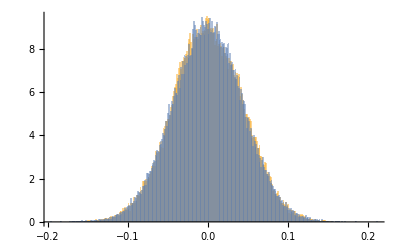

```mathematica
Histogram[{x112Re, x112Rerand}, 450, PDF]
```

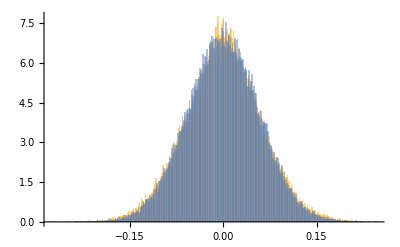

```mathematica
Histogram[{x433, x433rand}, 450, PDF]
```

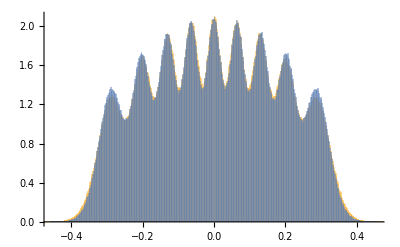

```mathematica
Histogram[{eig, randeig}, 450, PDF]
```

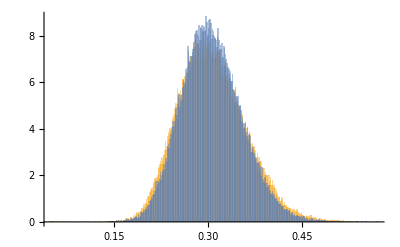

```mathematica
Histogram[{trX1sq, trX1sqrand}, 450, PDF]
```

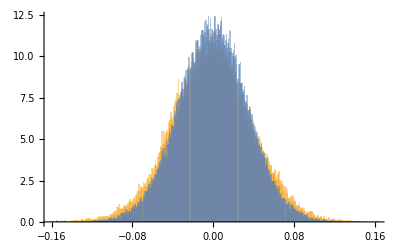

```mathematica
Histogram[{trX1X2, trX1X2rand}, 450, PDF
]
```

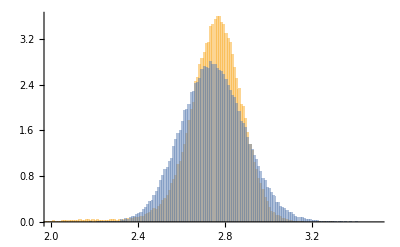

```mathematica
Histogram[{trXsq, trXsqrand}, 450, PDF,
PlotRange->{{2.0, 3.5}, Automatic}
]
```

```mathematica
Skewness[trXsq]
```

-1.81919

```mathematica
Skewness[trXsqrand]
```

0.102445

```mathematica
Kurtosis[trXsq]
```

16.808

```mathematica
Kurtosis[trXsqrand]
```

2.99759

```mathematica
CentralMoment[trXsq, 2]
```

0.0187114

```mathematica
CentralMoment[trXsqrand, 2]
```

0.0209416

```mathematica
CentralMoment[trXsq, 3]
```

-0.00465624

```mathematica
CentralMoment[trXsqrand, 3]
```

0.00031046

```mathematica
CentralMoment[trXsq, 4]
```

0.00588474

```mathematica
CentralMoment[trXsqrand, 4]
```

0.00131459